```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/2,maxt/2-maxt/10}];
```

```mathematica
pathToOutput=ToString["\..\plots\aperiodic1\\"];
```

## Step response

### TF function

```mathematica
k=10;
T=0.01;
maxt = 0.04;
TFsimple=10/(1+0.01 s);
TF=TransferFunctionModel[TFsimple,s];
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Horizontal Dashed Line

```mathematica
stepLineAbove=Line[{{0,TFstableValue},{maxt,TFstableValue}}];
```

### Tangent Line

```mathematica
a=0.001;
tangentLine =(D[TFstep,t]/.t->a)×(t-a) + (TFstep/.t->a);
```

### Vertical Dashed Line

```mathematica
sl=Solve[tangentLine==TFstableValue];
tangientInStable=sl[[All,1,2]][[1]];
vertLine=Line[{{tangientInStable,0},{tangientInStable,TFstableValue}}];
```

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Text@TraditionalForm@Style[text, 18,Plain,FontFamily->"Times"];
```

#### Horizontal size

```mathematica
(*horSizeLeft={0,TFstableValue+0.5};
horSizeRight={tangientInStable,TFstableValue+0.5};
horSize={arrowsHeads,Arrow[{horSizeLeft,horSizeRight}]};*)
horSizeText=Text[
sizeText["T"],
{
tangientInStable,
-0.5
}
];
```

#### Vertical size

```mathematica
(*verSizeX=(tangientInStable+maxt)/2;
verSizeStart={verSizeX,0};
verSizeEnd={verSizeX,TFstableValue};
verSize={arrowsHeads,Arrow[{verSizeStart,verSizeEnd}]};*)
verSizeText=Text[
sizeText["k"],
{
-0.0005,
TFstableValue
}
];
```

### Plot

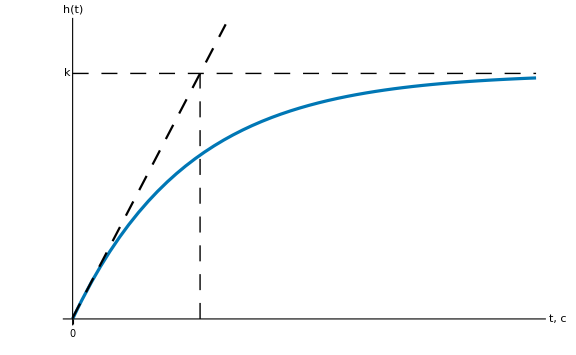

```mathematica
tickXStep=1/100;
tickYStep=1;

stepRespPic=Plot[{TFstep,tangentLine}, {t, 0, maxt},
LabelStyle->{FontFamily->"Arial",14,Black},
AxesLabel->{sizeText["t, с"],sizeText["h(t)"]},
GridLines->None,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt},{0,TFstableValue*1.2}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{
Prepend[(#&@Array[{tickXStep#,}&,100]),{0,0}],
(#&@Array[{tickYStep#,}&,100])
},
Epilog->{
{Directive[Black,dashingStyle],stepLineAbove},
{Directive[Black,dashingStyle],vertLine},
{horSizeText},
{verSizeText}
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"step.svg";
Export[fName,stepRespPic];
```

## Bode plot

### Approx

```mathematica
tfm=TFsimple;
minF=Log10[10];
maxF=Log10[1000];
cF1=Log10[100];
xcoords={minF,cF1,maxF};
mag0=20 Log10@Abs[tfm/.s->I 0.001];
ls={mag0,0,-20 (maxF-cF1)};
ycoords=FoldList[Plus,ls[[1]],ls[[2;;-1]]];
```

### Vert Line

```mathematica
wLine=Line[{
{cF1,mag0},
{cF1,0}
}];
```

### Log Plot

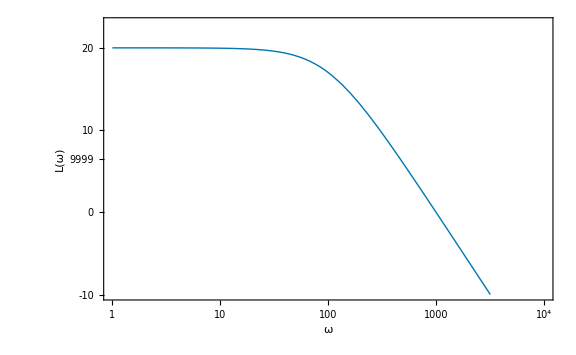

```mathematica
bodePlot=BodePlot[TF,{1,10^4},PlotRange->{{-10,23},Automatic},
PlotStyle->Thickness[0.004],
ImageSize->Large
];
ampBodePlot=RestylePlot[
bodePlot[[1,1,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-apm-freq.svg";
Export[fName,ampBodePlot]
```

D:\Wagnus Files\Complate Bullshit\5.1 - lust for life\V-courses\vgit\src\..\plots\aperiodic1\log-apm-freq.svg

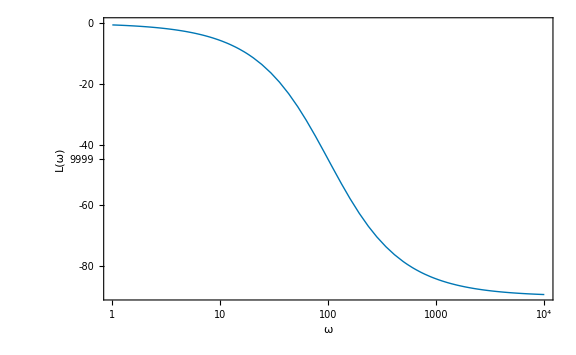

```mathematica
phaseBodePlot=RestylePlot[
bodePlot[[1,2,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-phase-freq.svg";
Export[fName,phaseBodePlot]
```

D:\Wagnus Files\Complate Bullshit\5.1 - lust for life\V-courses\vgit\src\..\plots\aperiodic1\log-phase-freq.svg

### Plot

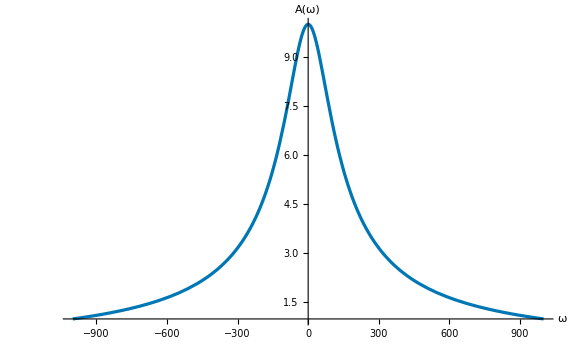

```mathematica
ampPlot=Plot[Abs[TF[I f]], {f, -1000, 1000},
(*PlotRange->{{0,Full},{0,10}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["A(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
(*Ticks->{
Prepend[(#&@Array[{100#,}&,100]),{0,0}],
(#&@Array[{2#,}&,100])
},*)
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"amp-freq.svg";
Export[fName,ampPlot]
```

D:\Wagnus Files\Complate Bullshit\5.1 - lust for life\V-courses\vgit\src\..\plots\aperiodic1\amp-freq.svg

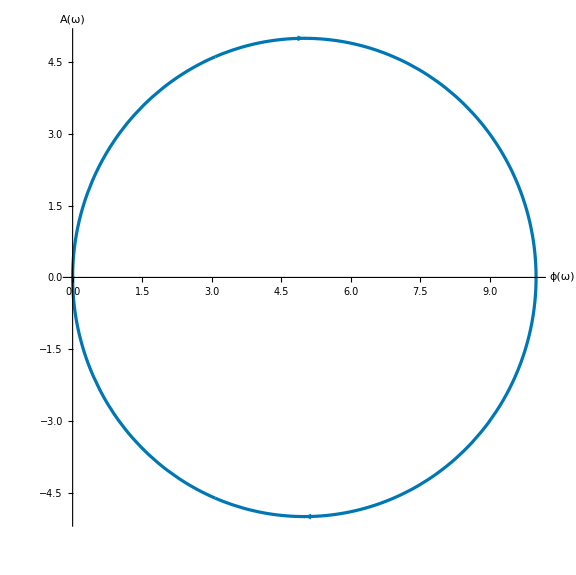

```mathematica
nyquistPlot=NyquistPlot[TF,
(*PlotRange->{{0,Full},{0,10}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ϕ(ω)"],sizeText["A(ω)"]},
AxesOrigin->{0,0},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"nyquist.svg";
Export[fName,nyquistPlot]
```

D:\Wagnus Files\Complate Bullshit\5.1 - lust for life\V-courses\vgit\src\..\plots\aperiodic1\nyquist.svg